```mathematica
(*s=InputString["Enter xml file name","tooth.xml"]//StringReplace[#," "->""]&;*)
xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive.xml"];
{tfifile,volumefile,legends,face,imagefilenames,txtfilenames,{featurefilename,visibilityfilename},resultxml,imagefile,rawfile,dataname}=xml;
(*Column[xml,Background->{{Lighter@LightYellow,Lighter@LightBlue}},Frame->True,FrameStyle->Directive[LightGray,Thin,Dashed]]*)

tf=Import[tfifile,"XML"];
bincount=256;
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//(RGBColor/@#&);
rgbfunction=(Blend[Transpose[{intensity,rgbcolors}], #1] & );
rgba=(#/255.&)/@Transpose[{r,g,b,a}]//(RGBColor/@#&);
rgbafunction=(Blend[Transpose[{intensity,rgba}], #1] & );
alpha=(#/255.&)/@a;

d = Import[volumefile,"Image3D"];
colorized=Image3D[d,ColorFunction->rgbafunction];
{lightness,chroma,hue,opacity}=ImageApply[List@@rgbafunction[#]&,d]//Image3D[#,ColorSpace->"RGB"]&//ColorSeparate[ColorConvert[#,"LCH"]]&;
(*lo=ImageMultiply[lightness,opacity];
co=ImageMultiply[chroma,opacity];*)
(*g1=ImageDifference[GaussianFilter[lightness,{2,Sqrt[2]/8.*2}],GaussianFilter[lightness,{4,Sqrt[2]/8.*4}]]
g2=ImageDifference[GaussianFilter[chroma,{2,Sqrt[2]/8.*2}],GaussianFilter[chroma,{4,Sqrt[2]/8.*4}]]
g3=ImageDifference[GaussianFilter[hue,{2,Sqrt[2]/8.*2}],GaussianFilter[hue,{4,Sqrt[2]/8.*4}]];
g4=ImageDifference[GaussianFilter[opacity,{2,Sqrt[2]/8.*2}],GaussianFilter[opacity,{4,Sqrt[2]/8.*4}]];*)
{g1,g2}=ParallelMap[ImageDifference[GaussianFilter[#,{2,Sqrt[2]/8.*2}],GaussianFilter[#,{4,Sqrt[2]/8.*4}]]&,{lightness,chroma}];

pos=intensity[[#]]&/@Position[alpha,_?(#==0&)];
index=Position[alpha,_?(#>0&)];
features=Table[ImageApply[If[#≥First[pos[[i]]] && #≤First[pos[[i+1]]],1,0]&,d],{i,1,Length[pos],2}];
chartcolors=rgbcolors[[#]]&/@Position[alpha,_?(#>0&)]//Flatten;
colorizedfeatures=ImageMultiply[colorized,#]&/@features;
viewpoints=<|"top":>Top,"back":>Back,"left":>Left,"bottom":>Bottom,"front":>Front,"right":>Right|>;
MapIndexed[Export[StringReplace[imagefile,"."->"_"<>ToString[First[#2]]<>"."],Show[#,Boxed->False,ViewPoint->viewpoints[face]]]&,colorizedfeatures];

intensity0=intensity;
alpha0=alpha;
rangeOfAlpha=Range[Length[alpha]];
If[First[intensity0]>0,intensity0=Join[{0},intensity0];alpha0=Join[{0},alpha0];rangeOfAlpha+=1];
If[Last[intensity0]<1,intensity0=Join[intensity0,{1}];alpha0=Join[alpha0,{0}]];
(*ListLinePlot[Transpose[{intensity0,alpha0}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
f=Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1];
(*Plot[f[x],{x,0,1},PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
index0=Position[alpha0,_?(#>0&)];
pos0=intensity0[[#]]&/@Position[alpha0,_?(#>0&)];
```

```mathematica
top:=Module[{list,count,img,list2,list3,tmp,d1},(* top *)
list=Image3DSlices[d,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d1=Image3D[list3]]
back:=Module[{list,count,img,list2,list3,tmp,d2},(* back *)
list=Image3DSlices[d,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
left:=Module[{list,count,img,list2,list3,tmp,d3},(* left *)
list=Image3DSlices[d,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
bottom:=Module[{list,count,img,list2,list3,tmp,d4},(* bottom *)
list=Reverse@Image3DSlices[d,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d4=Image3D[Reverse[list3]]]
front:=Module[{list,count,img,list2,list3,tmp,d5},(* front *)
list=Reverse@Image3DSlices[d,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
right:=Module[{list,count,img,list2,list3,tmp,d6},(* right *)
list=Reverse@Image3DSlices[d,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
renderslices=<|"top":>top,"back":>back,"left":>left,"bottom":>bottom,"front":>front,"right":>right|>;
```

```mathematica
target={0.1,0.3,0.6};
stepsize=0.01;
notfirstime=False;
```

```mathematica
(*list=Table[
vis=renderslices[face];
viss=ImageMultiply[g1,vis];(* weighted by lightness DoG (difference of Gaussians) *)
vs=ParallelTable[ImageMeasurements[ImageMultiply[viss,features[[i]]],"TotalIntensity"]/ImageMeasurements[viss,"TotalIntensity"],{i,Length[features]}];
viss2=ImageMultiply[g2,vis];(* weighted by chroma DoG *)
vs2=ParallelTable[ImageMeasurements[ImageMultiply[viss2,features[[i]]],"TotalIntensity"]/ImageMeasurements[viss2,"TotalIntensity"],{i,Length[features]}];
mean=Mean[{vs,vs2}];
pcount=Count[mean-target,_?(#>0&)];
ncount=Count[mean-target,_?(#<0&)];
pstep=If[pcount<1,1,pcount]*stepsize;
nstep=-If[ncount<1,1,ncount]*stepsize;
steps=ParallelTable[If[mean[[i]]>target[[i]],nstep,pstep],{i,Length[mean]}];
peaks=alpha0[[#]]&/@index0;
peaks=peaks+steps;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
f=Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1];
{mean,ParallelMap[f[#]&,pos0],RootMeanSquare[mean-target]}
,{40}];*)
```

```mathematica
(*list={};
rms0=Infinity;
rms=0;
While[rms<rms0,*)
list=Table[
vis=renderslices[face];
viss=ImageMultiply[g1,vis];(* weighted by lightness DoG (difference of Gaussians) *)
vs=ParallelTable[ImageMeasurements[ImageMultiply[viss,features[[i]]],"TotalIntensity"]/ImageMeasurements[viss,"TotalIntensity"],{i,Length[features]}];
viss2=ImageMultiply[g2,vis];(* weighted by chroma DoG *)
vs2=ParallelTable[ImageMeasurements[ImageMultiply[viss2,features[[i]]],"TotalIntensity"]/ImageMeasurements[viss2,"TotalIntensity"],{i,Length[features]}];
mean=Mean[{vs,vs2}];
pcount=Count[mean-target,_?(#>0&)];
ncount=Count[mean-target,_?(#<0&)];
pstep=If[pcount<1,1,pcount]*stepsize;
nstep=-If[ncount<1,1,ncount]*stepsize;
steps=ParallelTable[If[mean[[i]]>target[[i]],nstep,pstep],{i,Length[mean]}];
If[notfirstime && Norm[mean-First@previous]>0,steps=(target-mean)/(mean-First@previous)*Last@previous];
notfirstime=True;
peaks=alpha0[[#]]&/@index0;
peaks=Clip[peaks+steps,{0,1}];
previous={mean,steps};
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
f=Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1];
(*list=Append[list,{mean,ParallelMap[f[#]&,pos0],steps,RootMeanSquare[mean-target]}];
rms0=rms;
rms=RootMeanSquare[mean-target]
]*)
{mean,ParallelMap[f[#]&,pos0],steps,RootMeanSquare[mean-target]}
,{20}];
```

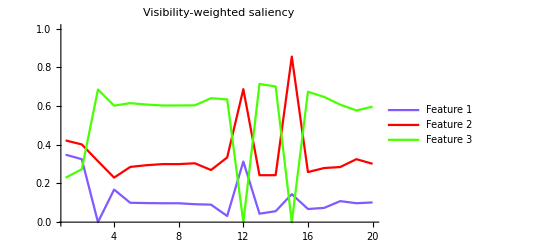

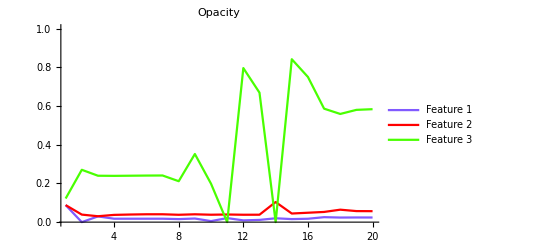

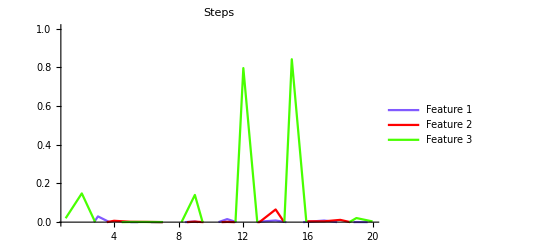

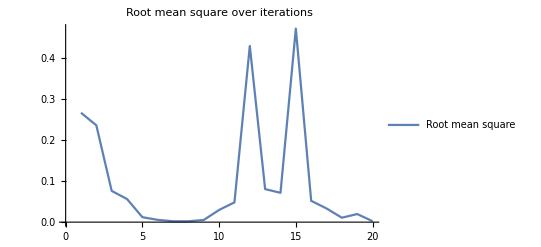

| Visibility-Weighted Saliency | Opacity | Steps | Root Mean Square
1 | 0.348509
0.42207
0.229394 | 0.0880392
0.0880392
0.121961 | -0.01
-0.01
0.02 | 0.267087
2 | 0.325149
0.401423
0.2734 | 0.
0.0389174
0.270394 | -0.096381
-0.0491218
0.148434 | 0.236394
3 | 0.
0.314876
0.685076 | 0.0296421
0.0304741
0.239719 | 0.0296421
-0.00844331
-0.030675 | 0.0762873
4 | 0.168164
0.230003
0.601789 | 0.0176269
0.0374375
0.239061 | -0.0120152
0.00696342
-0.000658808 | 0.0564186
5 | 0.0999433
0.285225
0.614787 | 0.0176369
0.0393006
0.23981 | 9.98559×10^-6
0.00186312
0.000749473 | 0.0120686
6 | 0.0984673
0.294058
0.607431 | 0.0176265
0.040554
0.240567 | -0.0000103692
0.00125343
0.000757073 | 0.00556403
7 | 0.0975282
0.299769
0.602659 | 0.0176538
0.0406048
0.240989 | 0.0000272917
0.000050735
0.000421904 | 0.00210034
8 | 0.0974943
0.299764
0.602698 | 0.0156361
0.0380006
0.21144 | -0.00201777
-0.00260419
-0.0295494 | 0.00213006
9 | 0.0925113
0.304026
0.603416 | 0.0186685
0.0404607
0.351975 | 0.00303242
0.00246012
0.140535 | 0.00529011
10 | 0.0903147
0.269354
0.640292 | 0.00529794
0.0382862
0.198422 | -0.0133705
-0.00217447
-0.153553 | 0.0297569
11 | 0.0317376
0.33414
0.634072 | 0.0208792
0.0394321
0. | 0.0155813
0.00114586
-0.841113 | 0.0482568
12 | 0.31304
0.686865
0. | 0.00907898
0.0381753
0.795916 | -0.0118002
-0.00125677
0.795916 | 0.430136
13 | 0.0435357
0.242401
0.714024 | 0.0115513
0.0383382
0.668815 | 0.00247229
0.000162866
-0.127102 | 0.0806378
14 | 0.056445
0.242544
0.700972 | 0.0198926
0.103787
0. | 0.00834132
0.0654486
-0.98327 | 0.0716323
15 | 0.144682
0.855271
0. | 0.0156687
0.0444753
0.841634 | -0.00422393
-0.0593115
0.841634 | 0.472695
16 | 0.0678102
0.258727
0.673427 | 0.0174374
0.0485789
0.749867 | 0.00176875
0.00410355
-0.0917674 | 0.0520613
17 | 0.0735138
0.279403
0.647049 | 0.0256511
0.0526668
0.586185 | 0.00821372
0.00408797
-0.163681 | 0.0333635
18 | 0.10849
0.284755
0.606723 | 0.0236574
0.0643125
0.558896 | -0.00199368
0.0116456
-0.0272891 | 0.0107966
19 | 0.0976513
0.325291
0.577026 | 0.0240895
0.0570467
0.580007 | 0.000432038
-0.00726582
0.021111 | 0.0197732
20 | 0.101806
0.301431
0.596731 | 0.0239017
0.0566109
0.58351 | -0.000187801
-0.000435805
0.00350266 | 0.00230923

```mathematica
saliency=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency",PlotRange->{All,{0,1}},PlotStyle->chartcolors]
Export[NotebookDirectory[]<>"saliency.png",saliency];
ListLinePlot[Transpose[Flatten[#2]&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity",PlotRange->{All,{0,1}},PlotStyle->chartcolors]
ListLinePlot[Transpose[#3&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Steps",PlotRange->{All,{0,1}},PlotStyle->chartcolors]
rms=ListLinePlot[#4&@@@list,PlotLegends->{"Root mean square"},PlotLabel->"Root mean square over iterations"]
TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity","Steps", "Root Mean Square"}}]
```

```mathematica
a2=IntegerPart[255*alpha0[[#]]]&/@rangeOfAlpha;
rgba2=(#/255.&)/@Transpose[{r,g,b,a2}]//(RGBColor/@#&);
intensity2=intensity0[[#]]&/@rangeOfAlpha;
rgbafunction2=(Blend[Transpose[{intensity2,rgba2}], #] & );
Image3D[d,ColorFunction->rgbafunction,ViewPoint->viewpoints[face]]
colorized2=Image3D[d,ColorFunction->rgbafunction2,ViewPoint->viewpoints[face]]
rgba2denormalized=Transpose[{r,g,b,a2}];
xrgba=Table[Join[{intensity2[[i]]},rgba2denormalized[[i]]],{i,Length[intensity2]}];
strlist={ToString[#1],ToString[#2],ToString[#3],ToString[#4],ToString[#5]}&@@@xrgba;
alphaMode=XMLElement["alphaMode",{"value"->"1"},{}];
gammaValue=XMLElement["gammaValue",{"value"->"1"},{}];
domain=XMLElement["domain",{"x"->"0","y"->"1"},{}];
threshold=XMLElement["threshold",{"x"->"0","y"->"1"},{}];
k=({int=XMLElement["intensity",{"value"->#1},{}],split=XMLElement["split",{"value"->"false"},{}],colorL=XMLElement["colorL",{"r"->#2,"g"->#3,"b"->#4,"a"->#5},{}]}&)@@@strlist;
keylist=XMLElement["key",{"type"->"TransFuncMappingKey"},{#1,#2,#3}]&@@@k;
keys=XMLElement["Keys",{},keylist];
TransFuncIntensity=XMLElement["TransFuncIntensity",{"type"->"TransFuncIntensity"},{alphaMode,gammaValue,domain,threshold,keys}];
VoreenData=XMLElement["VoreenData",{"version"->"1"},{TransFuncIntensity}];
xml=XMLObject["Document"][{XMLObject["Declaration"]["Version"->"1.0"],XMLObject["Comment"]["This is a Voreen transfer function exported from Mathematica"]},VoreenData,{}];
Export[NotebookDirectory[]<>"optimized.tfi",xml, "XML"];
```

-Graphics3D-

-Graphics3D-

```mathematica
ListLinePlot[Transpose[{intensity,alpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"Before optimization"]
(*Transpose[{intensity,r,g,b,a}]*)
ListLinePlot[Transpose[{intensity0[[#]]&/@rangeOfAlpha,alpha0[[#]]&/@rangeOfAlpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"After optimization"]
(*xrgba*)
```

-Graphics-

-Graphics-